# Phase Transition and Running Coupling in the Minimal SM

## Running Coupling

```mathematica
ClearAll["Global`*"]
```

## SM Parameters

```mathematica
sw = √0.23116;
cw = √(1 - sw^2);
mZ = 91.1876; 
mW = 80.399;
(*mtpole = 173.1-0.7*2.5;*)
GF = 1.16637 10^-5;
v=1/(√(√2*GF));
mb=4.19;mc=1.27;ms=0.1;
α0=1/137.035999679;
ΔαhmZ=0.02758;
αmZ= α0/(1-0.03150-ΔαhmZ+0.00007);
αsmZ=0.1181+0.0011*(1);

Mpl=2.4*10^18;(*Planck mass*)
mhpole=125.18+0.16*(0);

ye=2.8*10^-6;
yμ=5.9*10^-4;
yτ=1.0*10^-2;
yd=1.6*10^-5/2;
ys=3.1*10^-4/2;
yb=1.6*10^-2/2;
yu=7.4*10^-6/2;
yc=3.6*10^-3/2;
```

## Running

```mathematica
(*Phase space factor*)
κ=1/(16*Pi^2); 

(*numbers of flavors*)
nf=6;
ng=3;
z3=Zeta[3];

(*QCD colour factors*)
ca=3;
dR=3;
cf=4/3;
cr=1/2;

(*Beta function for top-Yukawa*)βyt[λ_,yt_,g3_,g2_,g1_]:=2*yt*(+κ*yt^2*(3/4+1/2*dR)+κ*g3^2*(-3*cf)+κ^2*λ^2*(3)+κ^2*yt^2*λ*(-6)+κ^2*yt^4*(3/4-9/4*dR)+κ^2*g3^2*yt^2*(6*cf+5/2*cf*dR)+κ^2*g3^4*(-3/2*cf^2-97/6*ca*cf+10/3*nf*cr*cf)+κ^3*λ^3*(-18)+κ^3*yt^2*λ^2*(285/8-45/4*dR)+κ^3*yt^4*λ*(63/2+45/2*dR)+κ^3*yt^6*(-345/32+107/32*dR+39/16*dR^2+9/4*z3+3/2*z3*dR)+κ^3*g3^2*yt^2*λ*(6*cf)+κ^3*g3^2*yt^4*(-57/2*cf-81/8*cf*dR)+κ^3*g3^4*yt^2*(471/16*cf^2-119/8*cf^2*dR+25*cr*cf+717/16*ca*cf+77/4*ca*cf*dR-33/4*nf*cr*cf-4*nf*cr*cf*dR-27*z3*cf^2+18*z3*cf^2*dR-27/2*z3*ca*cf-9*z3*ca*cf*dR)+κ^3*g3^6*(-129/2*cf^3+129/4*ca*cf^2-11413/108*ca^2*cf+46*nf*cr*cf^2+556/27*nf*ca*cr*cf+140/27*nf^2*cr^2*cf-48*z3*nf*cr*cf^2+48*z3*nf*ca*cr*cf))+yt κ(-9/4 g2^2-17/12 g1^2)+yt κ^2(5/2 yt^2(17/12 g1^2+9/4 g2^2)+yt^2(223/48 g1^2+135/16 g2^2)+25/9 g1^4(9/200+29/45*ng)-3/4 g1^2 g2^2+19/9 g1^2 g3^2-(35/4-ng)g2^4+9 g2^2 g3^2);

(*Beta function for the gauge couplings*)
βg3[λ_,yt_,g3_,g2_,g1_]:=2*g3*(+κ*g3^2*(-11/6*ca+2/3*nf*cr)+κ^2*g3^2*yt^2*(-2*cr)+κ^2*g3^4*(-17/3*ca^2+2*nf*cr*cf+10/3*nf*ca*cr)+κ^3*g3^2*yt^4*(9/2*cr+7/2*cr*dR)+κ^3*g3^4*yt^2*(-3*cr*cf-12*ca*cr)+κ^3*g3^6*(-2857/108*ca^3-nf*cr*cf^2+205/18*nf*ca*cr*cf+1415/54*nf*ca^2*cr-22/9*nf^2*cr^2*cf-79/27*nf^2*ca*cr^2))+g3^3 κ^2(11/6 g1^2+9/2 g2^2);
βg1[λ_,yt_,g3_,g2_,g1_]:=-g1^3 κ(-1/6-20/9*ng)+g1^3 κ^2 5/3(199/30 g1^2+27/10 g2^2+44/5 g3^2-17/10 yt^2);
βg2[λ_,yt_,g3_,g2_,g1_]:=-g2^3 κ(43/6-4/3*ng)+g2^3 κ^2(3/2 g1^2+35/6 g2^2+12 g3^2-3/2 yt^2);

(*Beta function for the quartic self-coupling of the scalar field*)
βλ[λ_,yt_,g3_,g2_,g1_]:=2*(+κ*λ^2*(12)+κ*yt^2*λ*(2*dR)+κ*yt^4*(-dR)+κ^2*λ^3*(-156)+κ^2*yt^2*λ^2*(-24*dR)+κ^2*yt^4*λ*(-1/2*dR)+κ^2*yt^6*(5*dR)+κ^2*g3^2*yt^2*λ*(10*cf*dR)+κ^2*g3^2*yt^4*(-4*cf*dR)+κ^3*λ^4*(3588+2016*z3)+κ^3*yt^2*λ^3*(291*dR)+κ^3*yt^4*λ^2*(789/2*dR-36*dR^2+252*z3*dR)+κ^3*yt^6*λ*(-1881/8*dR+80*dR^2-66*z3*dR)+κ^3*yt^8*(13/2*dR-195/8*dR^2-12*z3*dR)+κ^3*g3^2*yt^2*λ^2*(-306*cf*dR+288*z3*cf*dR)+κ^3*g3^2*yt^4*λ*(895/4*cf*dR-324*z3*cf*dR)+κ^3*g3^2*yt^6*(-19/2*cf*dR+60*z3*cf*dR)+κ^3*g3^4*yt^2*λ*(-119/2*cf^2*dR+77*ca*cf*dR-16*nf*cr*cf*dR+72*z3*cf^2*dR-36*z3*ca*cf*dR)+κ^3*g3^4*yt^4*(131/2*cf^2*dR+48*cr*cf*dR-109/2*ca*cf*dR+10*nf*cr*cf*dR-48*z3*cf^2*dR+24*z3*ca*cf*dR))+κ/2(-(3 g1^2+9 g2^2)2λ+9/4(1/3 g1^4+2/3 g1^2 g2^2+g2^4))+κ^2/2((54 g2^2+18 g1^2)4 λ^2-((313/8-10ng)g2^4-39/4 g2^2 g1^2-(687/200+2ng)25/9 g1^4)2λ+(497/8-8ng)g2^6-(97/40+8/5 ng)5/3 g2^4 g1^2-(717/200+8/5 ng)25/9 g2^2 g1^4-(531/1000+24/25 ng)125/27 g1^6-8/3 g1^2 2 yt^4-9/2 g2^4 yt^2+5/3 g1^2(63/5 g2^2-57/10 g1^2)yt^2+10*2 λ yt^2(17/12 g1^2+9/4 g2^2));

(*measured gauge coupling*)
g1mZ=(√(4π αmZ))/cw;
g2mZ=(√(4π αmZ))/sw;
g3mZ=√(4π*αsmZ);
αsmZ=0.1179;

(*Measured pole masses*)
mhpole=125.10;
mtpole=172.76;

(*MSbar couplings*)
λmtpole:=0.12604+0.00206*(mhpole-125.15)-0.00004(mtpole-173.34);
ytmtpole:=0.93690+0.00556(mtpole-173.34)-0.00003(mhpole-125.15)-0.00042((αsmZ-0.1184)/0.0007);
g3mtpole=1.1666+0.00314((αsmZ-0.1184)/0.0007)-0.00046(mtpole-173.34);
g2mtpole=0.64779+0.00004(mtpole-173.34)+0.00011*(mW-80.384)/0.014;
g1mtpole=0.35830+0.00011(mtpole-173.34)-0.00020*(mW-80.384)/0.014;
(*IW: should these equations be updated? These equations come from the near criticality paper, but that paper cites a measured value different from the current value*)
```

```mathematica
s:=NDSolve[{hλ'[t]==βλ[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t]],hyt'[t]==βyt[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t]],hg3'[t]==βg3[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t]],hg2'[t]==βg2[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t]],hg1'[t]==βg1[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t]],hλ[Log[mtpole/mZ]]==λmtpole,hyt[Log[mtpole/mZ]]==ytmtpole,hg3[Log[mtpole/mZ]]==g3mtpole,hg2[Log[mtpole/mZ]]==g2mtpole,hg1[Log[mtpole/mZ]]==g1mtpole},{hg1,hg2,hg3,hλ,hyt},{t,-6,17*Log[10]},MaxSteps->10^5];
```

```mathematica
{g1[μ_]}=hg1[Log[μ/mZ]]/.s;
{g2[μ_]}=hg2[Log[μ/mZ]]/.s;
{g3[μ_]}=hg3[Log[μ/mZ]]/.s;
{λ[μ_]}=hλ[Log[μ/mZ]]/.s;
{yt[μ_]}=hyt[Log[μ/mZ]]/.s;
```

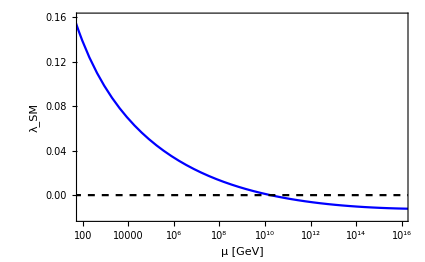

```mathematica
LogLinearPlot[{λ[μ],0},{μ,10,10^17},BaseStyle->{FontSize->16},Frame->True,FrameLabel->{Style["μ [GeV]",FontSize->18],Style["λ_SM",FontSize->18]},LabelStyle->{Black},PlotRange->{{100,10^16},{-0.02,0.16}},PlotStyle->{Blue,Directive[Dashed,Black]},FrameTicksStyle->{FontSize->18}]
```

## Phase Transitions

## Test effective potential at v_R=10^8 GeV

```mathematica
JB[x_]:=NIntegrate[z^2*Log[1-Exp[-Sqrt[z^2+x]]],{z,0,Infinity}]
(*bosonic field contributions*)
JF[x_]:=NIntegrate[z^2*Log[1+Exp[-Sqrt[z^2+x]]],{z,0,Infinity}]
(*fermionic field contributions*)
(*Cross check*)
fit11=Table[{ϕ,JB[ϕ]},{ϕ,10^(-1),200,.1}];
JBfit11[ϕ_]=Fit[fit11,{1,ϕ^0.5,ϕ,ϕ^2,ϕ^3,ϕ^1.5,ϕ^4,ϕ^5,ϕ^2.5,ϕ^3.5,ϕ^4.5,ϕ^5.5,ϕ^6,ϕ^6.5,ϕ^7,ϕ^7.5,ϕ^8,ϕ^9,ϕ^10,ϕ^11,ϕ^12,ϕ^13,ϕ^14,ϕ^15,ϕ^16,ϕ^17,ϕ^18,ϕ^19,ϕ^20},ϕ];
fit12=Table[{ϕ,JB[ϕ]},{ϕ,10^(-3),10^(-1),10^(-3)}];
JBfit12[ϕ_]=Fit[fit12,{1,ϕ^0.5,ϕ,ϕ^2,ϕ^3,ϕ^1.5,ϕ^4,ϕ^5,ϕ^2.5,ϕ^3.5,ϕ^4.5,ϕ^5.5,ϕ^6,ϕ^6.5,ϕ^7,ϕ^7.5,ϕ^8,ϕ^9,ϕ^10,ϕ^11,ϕ^12,ϕ^13,ϕ^14,ϕ^15,ϕ^16,ϕ^17,ϕ^18,ϕ^19,ϕ^20},ϕ];
fit13=Table[{ϕ,JB[ϕ]},{ϕ,0,10^(-3),10^(-6)}];
JBfit13[ϕ_]=Fit[fit13,{1,ϕ^0.5,ϕ,ϕ^2,ϕ^3,ϕ^1.5,ϕ^4,ϕ^5,ϕ^2.5,ϕ^3.5,ϕ^4.5,ϕ^5.5,ϕ^6,ϕ^6.5,ϕ^7,ϕ^7.5,ϕ^8,ϕ^9,ϕ^10,ϕ^11,ϕ^12,ϕ^13,ϕ^14,ϕ^15,ϕ^16,ϕ^17,ϕ^18,ϕ^19,ϕ^20},ϕ];
fit21=Table[{ϕ,JF[ϕ]},{ϕ,10^(-1),200,.1}];
JFfit21[ϕ_]=Fit[fit21,{1,ϕ^0.5,ϕ,ϕ^2,ϕ^3,ϕ^1.5,ϕ^4,ϕ^5,ϕ^2.5,ϕ^3.5,ϕ^4.5,ϕ^5.5,ϕ^6,ϕ^6.5,ϕ^7,ϕ^7.5,ϕ^8,ϕ^9,ϕ^10,ϕ^11,ϕ^12,ϕ^13,ϕ^14,ϕ^15,ϕ^16,ϕ^17,ϕ^18,ϕ^19,ϕ^20},ϕ];
fit22=Table[{ϕ,JF[ϕ]},{ϕ,10^(-3),10^(-1),10^(-3)}];
JFfit22[ϕ_]=Fit[fit22,{1,ϕ^0.5,ϕ,ϕ^2,ϕ^3,ϕ^1.5,ϕ^4,ϕ^5,ϕ^2.5,ϕ^3.5,ϕ^4.5,ϕ^5.5,ϕ^6,ϕ^6.5,ϕ^7,ϕ^7.5,ϕ^8,ϕ^9,ϕ^10,ϕ^11,ϕ^12,ϕ^13,ϕ^14,ϕ^15,ϕ^16,ϕ^17,ϕ^18,ϕ^19,ϕ^20},ϕ];
fit23=Table[{ϕ,JF[ϕ]},{ϕ,0,10^(-3),10^(-6)}];
JFfit23[ϕ_]=Fit[fit23,{1,ϕ^0.5,ϕ,ϕ^2,ϕ^3,ϕ^1.5,ϕ^4,ϕ^5,ϕ^2.5,ϕ^3.5,ϕ^4.5,ϕ^5.5,ϕ^6,ϕ^6.5,ϕ^7,ϕ^7.5,ϕ^8,ϕ^9,ϕ^10,ϕ^11,ϕ^12,ϕ^13,ϕ^14,ϕ^15,ϕ^16,ϕ^17,ϕ^18,ϕ^19,ϕ^20},ϕ];
JBfit[x_/;10^(-1)<x≤200]=JBfit11[x];
JBfit[x_/;10^(-3)<=x≤10^(-1)]=JBfit12[x];
JBfit[x_/;0<=x≤10^(-3)]=JBfit13[x];
JBfit[x_0/;200<x]=0;
JFfit[x_/;10^(-1)<x≤200]=JFfit21[x];
JFfit[x_/;10^(-3)<=x≤10^(-1)]=JFfit22[x];
JFfit[x_/;0<=x≤10^(-3)]=JFfit23[x];
JFfit[x_/;200<x]=0;
```

```mathematica
vRtest=10^8;
mttest=1/2 yt[vRtest]^2 vRtest^2;
mWtest=1/4 g2[vRtest]^2 vRtest^2;
mZtest=1/4(g2[vRtest]^2+g1[vRtest]^2)vRtest^2;
λtest=λ[vRtest]
mHtest=√(2λtest) vRtest;
yt[vRtest]
gtest=g2[vRtest]
g1test=g1[vRtest]
```

0.0133345

0.590319

0.586967

0.38811

```mathematica
Btest=3/(64 π^2 vRtest^4)(2 mWtest^2+mZtest^2-4 mttest^2);
Dtest=1/(8 vRtest^2)(2mWtest+mZtest+2mttest);
Etest=1/(4π vRtest^3)(2 mWtest^(3/2)+mZtest^(3/2));
Etestredeem=2/3 Etest;
T0test=√(1/(4Dtest)(mHtest^2-8Btest vRtest^2));
aB=Exp[3.91];
aF=Exp[1.14];
mgauge=({{gtest^2 x1^2/4+11/6 gtest^2 x2^2, -gtest g1test x1^2/4}, {-gtest g1test x1^2/4, g1test^2 x1^2/4+11/6 g1test^2 x2^2}});
gaugeL=Eigenvalues[mgauge]//FullSimplify;
mWL[ϕ_,T_]:=1/4 gtest^2 ϕ^2+11/6 gtest^2 T^2;(*longitudal mode for W+ and W-, or W1 and W2*)
mBL[ϕ_,T_]:=gaugeL[[1]]/.{x1->ϕ,x2->T};(*SM B particle, massless*)
mZL[ϕ_,T_]:=gaugeL[[2]]/.{x1->ϕ,x2->T};(*Zprime particle*)
λTtest[T_]:=λtest-3/(16 π^2 vRtest^4)(2 mWtest^2 Log[mWtest/(aB T^2)]+mZtest^2 Log[mZtest/(aB T^2)]-4 mttest^2 Log[mttest/(aF T^2)]);
resum[ϕ_,T_]:=T/(12π)(2((mWtest ϕ^2/vRtest^2)^(3/2)-mWL[ϕ,T]^(3/2))+((mZtest ϕ^2/vRtest^2)^(3/2)-(mZL[ϕ,T])^(3/2))-Abs[mBL[ϕ,T]]^(3/2));
V0[ϕ_,T_]:=-1/2 λtest vRtest^2 ϕ^2+λtest/4 ϕ^4+2Btest vRtest^2 ϕ^2-3/2 Btest ϕ^4+Btest ϕ^4 Log[ϕ^2/vRtest^2];(*T=0 form, with on-shell renormalization scheme*)
VFT[ϕ_,T_]:=T^4/(2 π^2)(6JBfit[(mWtest ϕ^2)/(T^2 vRtest^2)]+3JBfit[(mZtest ϕ^2)/(T^2 vRtest^2)]-12JFfit[(mttest ϕ^2)/(T^2 vRtest^2)]);
Vtestresum[ϕ_,T_]:=Dtest(T^2-T0test^2)ϕ^2-Etest T ϕ^3+λTtest[T]/4 ϕ^4+resum[ϕ,T]-resum[10^-10,T];(*High-T with resummation*)
Vredeem[ϕ_,T_]:=Dtest(T^2-T0test^2)ϕ^2-Etestredeem T ϕ^3+λTtest[T]/4 ϕ^4;(*High-T without resummation, but with 2/3 factor on the cubic term*)
Vfull[ϕ_,T_]:=V0[ϕ,T]+VFT[ϕ,T]+resum[ϕ,T]-(VFT[10^-10,T]+resum[10^-10,T]);(*Full form, with resummation*)
Vtest[ϕ_,T_]:=Dtest(T^2-T0test^2)ϕ^2-Etest T ϕ^3+λTtest[T]/4 ϕ^4;(*High-T without resummation, Dine's paper*)
Vfullnoresum[ϕ_,T_]:=V0[ϕ,T]+VFT[ϕ,T]-(VFT[10^-10,T]);(*Full form without resummation, Dine's paper*)
```

```mathematica
T0test
```

3.05803×10^7

```mathematica
FindRoot[T0test √((Dtest λTtest[T])/(-Etestredeem^2+Dtest λTtest[T]))==T,{T,T0test}](*Tc of the high-T formulation*)
```

{T→3.0917×10^7}

### Plot everything with resummation at T=T_c

```mathematica
Tplot=1.07582T0test
Plot[{Vtestresum[Tplot*ratio,Tplot],Vfull[Tplot*ratio,Tplot],Vredeem[0.93978*Tplot*ratio,0.93978*Tplot]},{ratio,0,1.2},PlotLegends->{"High-T with resum", "Full with resum", "High-T with redeemed cubic"},BaseStyle->{FontSize->16,FontFamily->"Times"},Frame->True,FrameLabel->{Style["ϕ/T",FontFamily->"Times",FontSize->18],Style["V_eff",FontFamily->"Times",FontSize->18]},LabelStyle->{Black},FrameTicksStyle->{Directive[FontFamily->"Times",FontSize->18]},ImageSize->500,PlotRangePadding->None,PlotRange->{{0,1.2},{-1*10^26,2*10^26}}]
```

3.28989×10^7

General::munfl: (7.95798×10^-37)^9 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (7.95798×10^-37)^10 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (7.95798×10^-37)^11 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics-

### Plot everything without resummation at T=T_c

```mathematica
Tplot=1.0254T0test;
Plot[{Vtest[Tplot*ratio,Tplot],Vfullnoresum[Tplot*ratio,Tplot]},{ratio,0,1.2},PlotLegends->{"High-T", "Full"},BaseStyle->{FontSize->16,FontFamily->"Times"},Frame->True,FrameLabel->{Style["ϕ/T",FontFamily->"Times",FontSize->18],Style["V_eff",FontFamily->"Times",FontSize->18]},LabelStyle->{Black},FrameTicksStyle->{Directive[FontFamily->"Times",FontSize->18]},ImageSize->500,PlotRangePadding->None,PlotRange->{{0,1.2},{-1*10^26,3*10^26}}]
```

General::munfl: (8.75983×10^-37)^9 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (8.75983×10^-37)^10 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (8.75983×10^-37)^11 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics-

Test result: Dine’s paper is correct. The high-T plus resummation agrees with the full-one. This seems to be reasonable. The 2/3 redeemed one gives smaller transition strength, and smaller Tc. 
The resummation reduced the phase transition strength.
I would suggest use the high-T with resummation.

## Find the scale where the strong 1st order PT is achieved

```mathematica
mtsq[vR_]:=1/2 yt[vR]^2 vR^2;
mWsq[vR_]:=1/4 g2[vR]^2 vR^2;
mZsq[vR_]:=1/4(g2[vR]^2+g1[vR]^2)vR^2;
λvR[vR_]:=λ[vR];
gvR[vR_]:=g1[vR];
mHvR[vR_]:=√(2λvR[vR]) vR;
B[vR_]:=3/(64 π^2 vR^4)(2 mWsq[vR]^2+mZsq[vR]^2-4 mtsq[vR]^2);
DD[vR_]:=1/(8 vR^2)(2mWsq[vR]+mZsq[vR]+2mtsq[vR]);
EE[vR_]:=1/(4π vR^3)(2 mWsq[vR]^(3/2)+mZsq[vR]^(3/2));
λTvR[vR_,T_]:=λvR[vR]-3/(16 π^2 vR^4)(2 mWsq[vR]^2 Log[mWsq[vR]/(aB T^2)]+mZsq[vR]^2 Log[mZsq[vR]/(aB T^2)]-4 mtsq[vR]^2 Log[mtsq[vR]/(aF T^2)]);
mgaugevR[vR_]:=({{g2[vR]^2 x1^2/4+11/6 g2[vR]^2 x2^2, -g1[vR] g2[vR] x1^2/4}, {-g2[vR]g1[vR] x1^2/4, g1[vR]^2 x1^2/4+11/6 g1[vR]^2 x2^2}});
gaugeLvR[vR_]=Eigenvalues[mgaugevR[vR]]//FullSimplify;
mWLvR[vR_,ϕ_,T_]:=1/4 g2[vR]^2 ϕ^2+11/6 g2[vR]^2 T^2;(*longitudal mode for W+ and W-, or W1 and W2*)
mBLvR[vR_,ϕ_,T_]:=gaugeLvR[vR][[1]]/.{x1->ϕ,x2->T};(*SM B particle, massless*)
mZLvR[vR_,ϕ_,T_]:=gaugeLvR[vR][[2]]/.{x1->ϕ,x2->T};(*Zprime particle*)
resumvR[vR_,ϕ_,T_]:=T/(12π)(2((mWsq[vR] ϕ^2/vR^2)^(3/2)-mWLvR[vR,ϕ,T]^(3/2))+((mZsq[vR] ϕ^2/vR^2)^(3/2)-(mZLvR[vR,ϕ,T])^(3/2))-Abs[mBLvR[vR,ϕ,T]]^(3/2));
T0vR[vR_]:=√(1/(4DD[vR])(mHvR[vR]^2-8B[vR] vR^2));
Veffrun[vR_,ϕ_,T_]:=DD[vR](T^2-T0vR[vR]^2)ϕ^2-EE[vR] T ϕ^3+λTvR[vR,T]/4 ϕ^4+resumvR[vR,ϕ,T]-resumvR[vR,10^-10,T];(*High-T with resummation*)
```

```mathematica
Tplot=1.07582T0vR[10^8];
Plot[Veffrun[10^8,ratio*Tplot,Tplot],{ratio,0,1.2},BaseStyle->{FontSize->16,FontFamily->"Times"},Frame->True,FrameLabel->{Style["ϕ/T",FontFamily->"Times",FontSize->18],Style["V_eff",FontFamily->"Times",FontSize->18]},LabelStyle->{Black},FrameTicksStyle->{Directive[FontFamily->"Times",FontSize->18]},PlotRangePadding->None,ImageSize->500,PlotRange->{{0,1.2},{-1*10^26,2*10^26}}]
```

-Graphics-

```mathematica
findstrengthTc[vR_]:=(
T1=Catch[Do[If[FindMinimum[Veffrun[vR,ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T0vR[vR],1.2T0vR[vR],0.1T0vR[vR]}]];
T2=Catch[Do[If[FindMinimum[Veffrun[vR,ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T1-0.1T0vR[vR],T1,0.01T0vR[vR]}]];
T3=Catch[Do[If[FindMinimum[Veffrun[vR,ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T2-0.01T0vR[vR],T2,0.001T0vR[vR]}]];
T4=Catch[Do[If[FindMinimum[Veffrun[vR,ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T3-0.001T0vR[vR],T3,0.0001T0vR[vR]}]];
Tc=Catch[Do[If[FindMinimum[Veffrun[vR,ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T4-0.0001T0vR[vR],T4,0.00001T0vR[vR]}]];
vev=ϕ/.FindMinimum[Veffrun[vR,ϕ,Tc],{ϕ,vR}][[2]];
strength=vev/Tc
)
```

```mathematica
vR=10^8;
Tc=3.2898639823989764*^7
FindMinimum[Veffrun[vR,ϕ,Tc],{ϕ,vR}][[2]]
```

3.28986×10^7

{ϕ→2.62363×10^7}

```mathematica
findstrengthTc[10^8]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMinimum::lstol will be suppressed during this calculation.

0.797488

```mathematica
list=Table[{logvR,findstrengthTc[10^logvR]},{logvR,8,10,0.5}]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMinimum::lstol will be suppressed during this calculation.

FindMinimum::sdprec: Line search unable to find a sufficient decrease in the function value with MachinePrecision digit precision.

General::stop: Further output of FindMinimum::sdprec will be suppressed during this calculation.

{{8.,0.797488},{8.5,1.05525},{9.,1.47483},{9.5,2.21891},{10.,3.54977}}

```mathematica
enhance[logvR_]:=Interpolation[list][logvR]
```

```mathematica
sol=Solve[enhance[logvR]==1.0,logvR]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{logvR→8.40713}}

```mathematica
10^logvR/.sol
```

{2.55344×10^8}

This is the symmetry breaking scale where the phase transition becomes SFOPT.